```mathematica
sbox="E4D12FB83A6C5907"


sbox=MIDORIsbox1="1053e2f7da9bc846"
sbox=MIDORIsbox0="cad3ebf789150246"
sbox=PRESENTsbox="C56B90AD3EF84712"
sbox=INVARIANTIsbox="07b3d596821eafc4"

ff[x1_,x2_,x3_,x4_]:={x1 +x2 x4,x2+x4+x3,x3,x3+x2}

(*ff[x1_,x2_,x3_,x4_]:={x1 x2 +1,x2+x3,x3,x1+x4}*)
permutation={1,5,9,13,2,6,10,14,3,7,11,15,4,8,12,16}

l=4;m=4;Nr=4;
ClearAll[S]
(*S[x_]:=S[x]=IntegerDigits[FromDigits[sbox,16],16,16][[x+1]]*)
S[x_]:=S[x]=FromDigits[Mod[ff@@IntegerDigits[x,2,4],2],2]

fmap=Table[{i,S[i]},{i,0,15}];
fimage=Map[Last,fmap];
fmap//TableForm
Union@fmap
Print["invertibility test:",Length[Union@fimage]==2^m]
```

E4D12FB83A6C5907

1053e2f7da9bc846

cad3ebf789150246

C56B90AD3EF84712

07b3d596821eafc4

{1,5,9,13,2,6,10,14,3,7,11,15,4,8,12,16}

0 | 0
1 | 4
2 | 7
3 | 3
4 | 5
5 | 9
6 | 2
7 | 14
8 | 8
9 | 12
10 | 15
11 | 11
12 | 13
13 | 1
14 | 10
15 | 6

{{0,0},{1,4},{2,7},{3,3},{4,5},{5,9},{6,2},{7,14},{8,8},{9,12},{10,15},{11,11},{12,13},{13,1},{14,10},{15,6}}

invertibility test:True

```mathematica
ff[x1,x2,x3,x4]
```

{x1+x2 x4,x2+x3+x4,x3,x2+x3}

```mathematica
IntegerDigits[S[1],2,4]
```

{0,1,1,0}

4

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15}

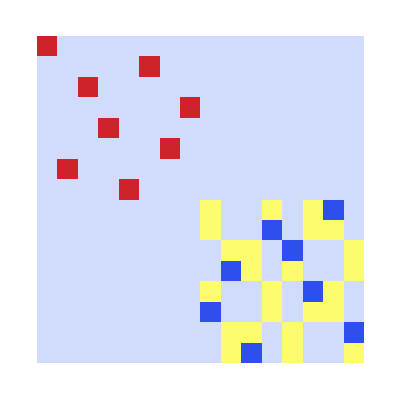

```mathematica
ClearAll[LAT,T,DDT,DDT2]
T[f_,a_,b_][x_]:=(-1)^(DigitCount[BitAnd[a,x],2,1]+DigitCount[BitAnd[b,f[x]],2,1])
T[f_,a_,b_][x_]:=Mod[(DigitCount[BitAnd[a,x],2,1]+DigitCount[BitAnd[b,f[x]],2,1]),2]


n=4
dom=Range[0,2^n-1]
LAT[f_]:=Table[2^n-Plus@@Map[T[f,a,b],dom],{a,0,2^n-1},{b,0,2^n-1}]
Without0[matrix_]:=Transpose[Drop[Transpose[Drop[matrix,1]],1]]
ArrayPlot[LAT[S],ColorFunction->"TemperatureMap"]
```

```mathematica
LAT[S]//TableForm
```

16 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 16 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 16 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 16 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 16 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 16 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 16 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 16 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 12 | 8 | 8 | 12 | 8 | 12 | 4 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 12 | 8 | 8 | 4 | 8 | 12 | 12 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 12 | 12 | 8 | 4 | 8 | 8 | 12
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 4 | 12 | 8 | 12 | 8 | 8 | 12
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 12 | 8 | 8 | 12 | 8 | 4 | 12 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 4 | 8 | 8 | 12 | 8 | 12 | 12 | 8
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 12 | 12 | 8 | 12 | 8 | 8 | 4
8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 8 | 12 | 4 | 8 | 12 | 8 | 8 | 12

```mathematica
(* calcolo degli autovalori -- autovettori ~ spazi invarianti (con probabilita') => utilizzabili come distinguisher *)

Position[LAT[S],12]-1
```

{{1,15},{3,13},{5,9},{7,11},{8,14},{10,12},{12,8},{14,10}}

```mathematica
dom=Range[0,2^n-1]

RowDDT[f_,dx_]:=Map[(BitXor[f[BitXor[#,dx]],f[#]])&,dom]
RowDDT2[f_,dx_]:=Map[{dx+1,#[[1]]+1}->#[[2]]&,Tally[RowDDT[f,dx]]]
```

```mathematica
ClearAll[DDT]
sparseDDT[f_]:=Flatten@Map[RowDDT2[f,#]&,dom]
DDT[f_]:=Normal[SparseArray[sparseDDT[f]]]
DDT[S]/2^n//MatrixForm
difference=Max[mm=Without0[DDT[S]]]
ArrayPlot[mm,ColorFunction->"TemperatureMap"]
```

```mathematica
characteristics=sparseDDT[S]
```

```mathematica
Normal[SparseArray@sparseDDT[S]]//MatrixForm
```

```mathematica
DeltaY[indices_]:=Select[Table[{Plus@@(2^(4-Map[First,Select[indices,#[[2]]==box&]])),box},{box,1,4}],#[[1]]=!=0&]

TargetNode[char1_,box1_]:=Module[{},(dx1=char1[[1,1]];
dy1=char1[[1,2]];
weigth1=char1[[2]];
indexes1=Flatten@Position[IntegerDigits[dy1,2,n],1];
(*permuto gli indici*)pindexes1=Map[{box1,#}&,indexes1];
DirectedEdge[{{dx1,box1}},DeltaY[pindexes1],weigth1])]

TargetNode[char1_,box1_,char2_,box2_]:=Module[{},(dx1=char1[[1,1]];
dy1=char1[[1,2]];
weigth1=char1[[2]];
indexes1=Flatten@Position[IntegerDigits[dy1,2,n],1];
(*permuto gli indici*)pindexes1=Map[{box1,#}&,indexes1];
dx2=char2[[1,1]];
dy2=char2[[1,2]];
weigth2=char2[[2]];
indexes2=Flatten@Position[IntegerDigits[dy2,2,n],1];
(*permuto gli indici---specifico all'SPN del libro*)pindexes2=Map[{box2,#}&,indexes2];
joinedindexes=Join[pindexes1,pindexes2];
DirectedEdge[{{dx1,box1},{dx2,box2}},DeltaY[joinedindexes],weigth1 weigth2/2^n])]


MakeEdges[node_?(Length[#]===1&)]:=Module[{dx,box,edges},((*Print["unario"];*){dx,box}=node[[1]];
edges=Map[TargetNode[#,box]&,Select[sparseDDT[S],#[[1,1]]==dx+1&]];
Select[edges,0<Length[#[[2]]]<=2&])]

MakeEdges[node_?(Length[#]===2&)]:=Module[{dx1,dx2,box1,box2,rowdx1,rowdx2,edges},((*Print["binario"];*){{dx1,box1},{dx2,box2}}=node;
(*seleziono le caratteristiche non-nulle della differenza in ingresso dx*)rowdx1=Select[sparseDDT[S],#[[1,1]]==dx1+1&];
rowdx2=Select[sparseDDT[S],#[[1,1]]==dx2+1&];
(*formo un arco tra la differenza in ingresso e ognuna delle differenze in uscita derivate dalle coppie di caratteristiche in entrata*)edges=Map[TargetNode[#[[1]],box1,#[[2]],box2]&,Tuples[{rowdx1,rowdx2}]];
(*seleziono quelle con solo 2 sbox attive in uscita*)Select[edges,0<Length[#[[2]]]<=2&])]
```

```mathematica
V={};

newedges={};newnodes={};edges={};
PickNode[nodes_]:=Module[{i},(i=RandomInteger[{1,Length[Q]}];
(*Print[i];*){Q[[i]],Drop[Q,{i}]})]

boxes=Range[1,4];
deltas=Range[0,2^n-1];
Q=Map[{#}&,Tuples[{deltas,boxes}]];Length[Q]
```

```mathematica
While[Length[Q]<400&&Length[Q]>0,(Print[Length[Q]];
{node,Q}=PickNode[Q];
(*Print["->",node];*)V=Append[V,node];
newedges=MakeEdges[node];
Print[newedges];
newnodes=Complement[Map[#[[2]]&,newedges],V];
Q=Join[Q,newnodes];
edges=Union[Join[edges,newedges]];
(*Print[Graph[edges]]*))]
```

```mathematica
Graph[edges]
```

```mathematica
cyc=FindCycle[Graph@edges,Infinity,All]
```

```mathematica
cc=ConnectedComponents[Graph[edges]];
HighlightGraph[Graph@edges,cyc]
```

```mathematica
cyc
```

```mathematica
S[2]
```

```mathematica
fspace=Range[0,4^16-1];
```

```mathematica
ClearAll[F]
```

```mathematica
F[f_][a_]:=IntegerDigits[f,4,16][[a+1]]
```

```mathematica
image=Map[FromDigits[Table[Mod[F[#][S[x]]+F[#][x],4],{x,0,2^4-1}],2]&,fspace];
Length[image]
Length[Union[image]]
```

```mathematica
F[5][1]
```

```mathematica
Table[Mod[F[5][S[x]]+F[5][x],2],{x,0,2^4-1}]
```

```mathematica
T0=Flatten[Position[image,0]]-1
T1=Flatten[Position[image,2^16-1]]-1
```

```mathematica
Map[Table[Mod[F[#][S[x]]+F[#][x],2],{x,0,2^4-1}]&,T0]
```

```mathematica
IrreduciblePolynomialQ[x^2+2x+2,Modulus->3]
```

True